# Geodesics Equation Solver

## Kerr’s Spacetime

## Manual calculation of the geodesics equations

```mathematica
Clear["Global`*"]
ClearAll[r,θ,ϕ,t,s]


ρ=r^2+a^2 Cos[θ]^2; 
Δ=r^2-2 m r+a^2;

(*Usual Boyer-Lindquist*)
metric=-{{-ρ/Δ,0,0,0},{0,-ρ,0,0},{0,0,-(((r^2+a^2)^2-Δ a Sin[θ]^2)/ρ) Sin[θ]^2,(a Sin[θ]^2( r^2 +a^2-Δ))/ρ},{0,0,(a Sin[θ]^2( r^2 +a^2-Δ))/ρ,(Δ-a^2 Sin[θ]^2)/ρ}};

(*From one of professors book*)
(*metric={{-ρ^2/Δ,0,0,0},{0,-ρ^2,0,0},{0,0,-(r^2+a^2) Sin[θ]^2-(2 m r a^2 Sin[θ]^4)/ρ^2,((2 m a r) Sin[θ]^2)/ρ^2},{0,0,((2 m a r) Sin[θ]^2)/ρ^2,1-(2 m r)/ρ^2}};*)

(*Eddington-Finkelstein*)
(*metric={{0,0,a Sin[θ]^2,-1},{0,-ρ^2,0,0},{a Sin[θ]^2,0,-(r^2+a^2) Sin[θ]^2-(2 m r a^2 Sin[θ]^4)/ρ^2,((2 m a r) Sin[θ]^2)/ρ^2},{-1,0,((2 m a r) Sin[θ]^2)/ρ^2,1-(2 m r)/ρ^2}}; *)
(* Com coordenadas (r,θ,ϕ,ν)*)


inversemetric = Simplify[Inverse[metric]];
coord={r,θ,ϕ,t};
christ[i_,j_,k_]:=christ[i,j,k]=Simplify[Sum[1/2 inversemetric[[i,d]] (D[metric[[d,k]],coord[[j]]]+D[metric[[d,j]],coord[[k]]]-D[metric[[j,k]],coord[[d]]]),{d,1,4}]]
```

```mathematica
eq=Table[coord[[i]]''+Sum[christ[i,j,k] coord[[j]]' coord[[k]]',{j,1,4},{k,1,4}],{i,1,4,1}];
eqs=eq/. {r''->r''[s],θ''->θ''[s],ϕ''->ϕ''[s],t''->t''[s],r'->r'[s],θ'->θ'[s],ϕ'->ϕ'[s],t'->t'[s],r->r[s],θ->θ[s],ϕ->ϕ[s],t->t[s]};
```

## Solving the equations

```mathematica
initFromELQ[E0_,Lz0_,Q0_,r0_,th0_,pr_,pθ_,a0_,m0_]:=Module[{Delta,rho2,Rr,ThetaTh,dr,dr2,dth,dth2,dt,dph,det,sinth2,costh2,csc2,gtt,gtϕ,grr,gϕϕ,gθθ},

Delta=r0^2-2 m0 r0+a0^2;
rho2=r0^2+a0^2 Cos[th0]^2;
sinth2=Sin[th0]^2;
costh2=Cos[th0]^2;
csc2=1/sinth2;

{grr,gθθ,gϕϕ,gtϕ,gtt}={metric[[1,1]],metric[[2,2]],metric[[3,3]],metric[[3,4]],metric[[4,4]]} /. {r->r0,θ->th0,m->m0,a->a0};
det=gtϕ^2-gtt*gϕϕ;

dt=(gϕϕ*E0+gtϕ*Lz0)/det;
dph=(-gtϕ*E0-gtt*Lz0)/det;
dth2= Q0-costh2(a0^2(1-E0^2)+(Lz0^2 *csc2));
dth=Sqrt[dth2/gθθ];
(*dr2=-1-gtt*dt^2-2*gtϕ*dt*dph-gϕϕ*dph^2-gθθ*dth^2;
dr=-Sqrt[dr2/grr];*)
Rr=((r0^2+a0^2)*E0-a0*Lz0)^2-Delta*(Q0+(Lz0-a0*E0)^2+r0^2);
dr=Rr/rho2^2;

(*dth=pθ/rho2;
dr=(Delta/rho2)pr;*)

{t[0]==0,r[0]==r0,θ[0]==th0,ϕ[0]==0,t'[0]==dt,r'[0]==dr,θ'[0]==dth,ϕ'[0]==dph}];



(*INIT CONDITIONS*)
E0=1;L0=2.082;Q=1.6;r0=5;th0=Pi/3;pr=0;pθ=1.9;a0=0.9;m0=1;

EQ=Table[eqs[[i]]==0/. {m->m0,a->a0},{i,1,4}];
Radius=2;
values ={};
sSingular=1000;
initConds= initFromELQ[E0,L0,Q,r0,th0,pr,pθ,a0,m0];

If[Im[ initConds[[6]]] !=0,initConds[[6]]=0];
If[Im[ initConds[[7]]] !=0,initConds[[7]]=0];
initConds

kerr=NDSolve[{EQ, initConds
},
{r,θ,ϕ,t},
{s,0,sSingular},
Method->{"StiffnessSwitching"},MaxStepSize->0.01,
AccuracyGoal->10,PrecisionGoal->10,
StepMonitor :> AppendTo[values,{r[s],θ[s],ϕ[s],t[s]}]
];

{rFunc,θFunc,ϕFunc}={r,θ,ϕ}/. kerr[[1]];
domain=First@rFunc["Domain"]


trajectory=ParametricPlot3D[{Sqrt[a0^2+rFunc[s]^2]*Sin[θFunc[s]]*Cos[ϕFunc[s]],Sqrt[a0^2+rFunc[s]^2]*Sin[θFunc[s]]*Sin[ϕFunc[s]],rFunc[s]*Cos[θFunc[s]]},{s,0,domain[[2]]},ColorFunction->Hue,AxesLabel->{"x","y","z"},PlotRange->Automatic,RegionFunction->Function[{x,y,z,s},Sqrt[x^2+y^2+z^2]>10^-8],Exclusions->None];
```

{t[0]==0,r[0]==5,θ[0]==π/3,ϕ[0]==0,t'[0]==1.60064,r'[0]==0.205154,θ'[0]==0.0784464,ϕ'[0]==0.128711}

{0.,1000.}

-Graphics3D-

-Graphics3D-

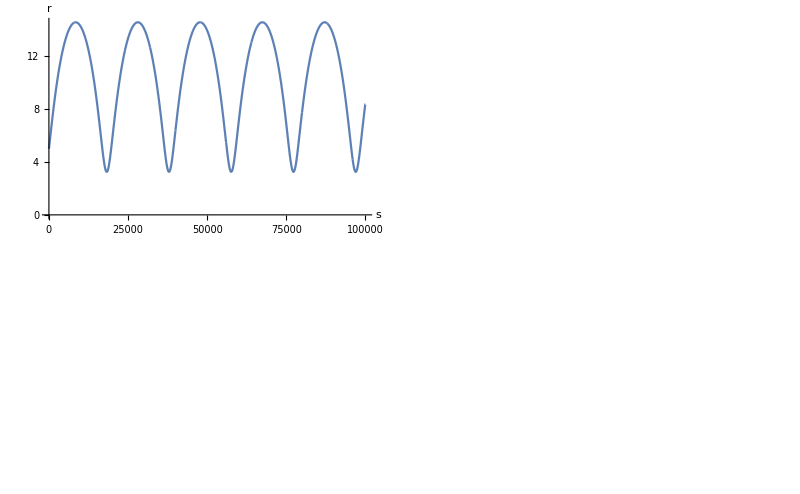

```mathematica
(*Kerr's black hole representation*)


(*Ring Singularity*)
Singularity = ParametricPlot3D[{a0*Cos[ϕ],a0*Sin[ϕ],0},{ϕ,0,2 Pi},PlotStyle->{Red}];

(*Infinite red shift surfaces*)
rSplus[θ_] := m0+Sqrt[m0^2-a0^2 Cos[θ]^2];
rSminus[θ_] := m0-Sqrt[m0^2-a0^2 Cos[θ]^2];

Ergosphere =ParametricPlot3D[{
{(Sqrt[rSplus[θ]^2+a0^2] Sin[θ] Cos[φ]),(Sqrt[rSplus[θ]^2+a0^2] Sin[θ] Sin[φ]),(rSplus[θ]Cos[θ])},(*Outer horizon*)
{(Sqrt[rSminus[θ]^2+a0^2] Sin[θ] Cos[φ]),(Sqrt[rSminus[θ]^2+a0^2] Sin[θ] Sin[φ]),(rSminus[θ]Cos[θ])}  (*Inner horizon*)
},
{θ,0,Pi},{φ,0,2 Pi},
PlotStyle->{Directive[Green,Opacity[0.1]],(*Outer horizon*)
		     Directive[Blue,Opacity[0.3]]    (*Inner horizon*)},
Mesh->None];

(*Event Horizons (2 if a^2<m^2) r_(+-)=r+-(m^2-a^2 cos^2 θ)^(1/2)*)
rHplus=m0+Sqrt[m0^2-a0^2];
rHminus=m0-Sqrt[m0^2-a0^2];

EventHorizon =ParametricPlot3D[{
{(Sqrt[rHplus^2+a0^2] Sin[θ] Cos[φ]),(Sqrt[rHplus^2+a0^2] Sin[θ] Sin[φ]),(rHplus *Cos[θ])},(*Outer horizon*)
{(Sqrt[rHminus^2+a0^2] Sin[θ] Cos[φ]),(Sqrt[rHminus^2+a0^2] Sin[θ] Sin[φ]),(rHminus*Cos[θ])}  (*Inner horizon*)
},
{θ,0,Pi},{φ,0,2 Pi},
PlotStyle->{Directive[Gray,Opacity[0.2]],(*Outer horizon*)
		     Directive[Gray,Opacity[0.5]]    (*Inner horizon*)},
Mesh->None];




Show[Singularity, EventHorizon, Ergosphere,PlotRange->All]

Show[trajectory,Singularity, EventHorizon, Ergosphere,PlotRange->{{-15,15},{-15,15},{-15,15}}]
(*{{-10,10},{-10,10},{-10,10}}*)

Manipulate[
ParametricPlot3D[{Sqrt[a0^2+rFunc[s]^2]*Sin[θFunc[s]]*Cos[ϕFunc[s]],Sqrt[a0^2+rFunc[s]^2]*Sin[θFunc[s]]*Sin[ϕFunc[s]],rFunc[s]*Cos[θFunc[s]]},{s,0,τ},AxesLabel->{"x","y","z"},PerformanceGoal->"Quality",PlotRange->{{-15,15},{-15,15},{-15,15}},Exclusions->None],{τ,1,domain[[2]]}]

GraphicsGrid[{
{ListLinePlot[values[[All,1]],PlotRange->Automatic,AxesLabel->{"s","r"}],
ListLinePlot[values[[All,2]],PlotRange->All,AxesLabel->{"s","θ"}]
},{ListLinePlot[values[[All,3]],PlotRange->All,AxesLabel->{"s","ϕ"}],
ListLinePlot[values[[All,4]],PlotRange->All,AxesLabel->{"s","t"}]
}}]
```

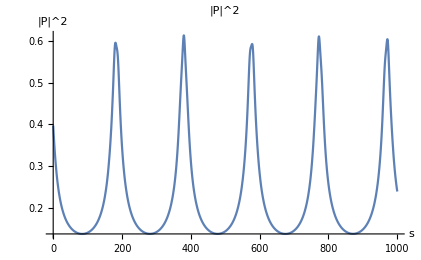

772.269

-Graphics3D-

```mathematica
(*Primer*)
U[s_]:={r'[s],θ'[s],ϕ'[s],t'[s]}/. kerr[[1]];
primer[s_]:=E0*U[s]-{0,0,0,1};  (*Kronecker delta:only t component gets-1*)
(*P2[s_] :=Sum[metric[[mu,nu]]*primer[s][[mu]]*primer[s][[nu]],{mu,1,4},{nu,1,4}] /. {r->rFunc[s],θ->θFunc[s], m->m0};*)
P2[s_] := metric[[4,4]]+2*E0^2-E0/. {r->rFunc[s],θ->θFunc[s], m->m0, a->a0};
primerPlot=Plot[P2[s],{s,0,domain[[2]]},PlotLabel->"|P|^2",PlotRange->All,AxesLabel->{"s","|P|^2"}]
sMax=NArgMax[{P2[s],5<s<1000},s];
sMax
maxPmag=Sqrt[P2[sMax]];

maxPoint={Sqrt[a0^2+rFunc[sMax]^2] Sin[θFunc[sMax]] Cos[ϕFunc[sMax]],Sqrt[a0^2+rFunc[sMax]^2] Sin[θFunc[sMax]] Sin[ϕFunc[sMax]],rFunc[sMax] Cos[θFunc[sMax]]};

marker=Graphics3D[{Red,Sphere[maxPoint,0.3]}];

Show[trajectory,Singularity, EventHorizon, Ergosphere,marker,PlotRange->{{-15,15},{-15,15},{-15,15}}]
```